# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

## Setup

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01","2022-11-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{BA.2,BA.2.3.20,BA.2.75,BA.2.75.2,BA.4.6,BA.5,BA.5.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.2,BA.5.1.22,BA.5.1.23,BA.5.1.27,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.2,BA.5.2.1,BA.5.2.20,BA.5.2.21,BA.5.2.23,BA.5.2.34,BA.5.2.6,BA.5.2.9,BA.5.5,BA.5.5.1,BA.5.6,BA.5.9,BE.1,BE.1.1,BE.3,BF.10,BF.11,BF.13,BF.26,BF.5,BF.7,BF.7.4,BK.1,BM.1.1,BN.1,BN.1.3,BQ.1,BQ.1.1,BQ.1.10,BQ.1.11,BQ.1.12,BQ.1.1.3,BQ.1.13,BQ.1.1.4,BQ.1.14,BQ.1.1.5,BQ.1.2,BQ.1.3,BQ.1.6,other,XBB.1}

```mathematica
n=Length[variants]
```

59

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

54

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

5

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

59

### Variant to clade mapping and clade colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
variantToClade=Map[#[[1]]->#[[2]]&,Drop[Import["../../data/pango-countries/pango_aliasing.tsv"],1]];
```

```mathematica
clades={"other","21L (Omicron)","22A (Omicron)","22B (Omicron)","22C (Omicron)","22D (Omicron)","22E (Omicron)","22F (Omicron)"};
```

```mathematica
cladeColors=Prepend[makeColors[Length[clades]-1],Gray]
```

{GrayLevel[0.5],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.54357188, 0.73433536, 0.41441192],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
cladeToColor=MapThread[#1->#2&,{clades,cladeColors}]
```

{other→GrayLevel[0.5],21L (Omicron)→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],22A (Omicron)→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],22B (Omicron)→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],22C (Omicron)→RGBColor[0.54357188, 0.73433536, 0.41441192],22D (Omicron)→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],22E (Omicron)→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

### Colors

```mathematica
colorMappingForClade[clade_]:=Module[{pos,shades,tints,col},
pos=Flatten[Position[variants,x_/;(x/.variantToClade)==clade]];
If[Length[pos]>0,
shades=Reverse[Table[Darker[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}]];
tints=Drop[Table[Lighter[clade/.cladeToColor,x],{x,0,0.5,1/(Length[pos])}],1];
col=Join[shades,tints];
Table[variants[[pos[[i]]]]->col[[i]],{i,Length[pos]}],
{}
]
]
```

```mathematica
variantColorMapping=Flatten[Map[colorMappingForClade,clades]]
```

{other→RGBColor[0.5, 0.5, 0.5],BA.2→RGBColor[0.1715652, 0.057908600000000005, 0.31848920000000003],BA.2.3.20→RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],BA.4.6→RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],BA.5→RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],BA.5.1→RGBColor[0.18487806444444443, 0.3391806040740741, 0.3500400681481482],BA.5.1.1→RGBColor[0.1946084888888889, 0.3570322148148148, 0.3684632296296297],BA.5.1.10→RGBColor[0.20433891333333332, 0.3748838255555555, 0.38688639111111117],BA.5.1.18→RGBColor[0.21406933777777776, 0.39273543629629626, 0.40530955259259266],BA.5.1.2→RGBColor[0.22379976222222223, 0.410587047037037, 0.42373271407407415],BA.5.1.22→RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],BA.5.1.23→RGBColor[0.24326061111111108, 0.4462902685185185, 0.46057903703703706],BA.5.1.27→RGBColor[0.2529910355555555, 0.4641418792592592, 0.47900219851851855],BA.5.1.30→RGBColor[0.26272145999999996, 0.48199348999999997, 0.49742536000000004],BA.5.1.5→RGBColor[0.27245188444444446, 0.49984510074074073, 0.5158485214814815],BA.5.2→RGBColor[0.28218230888888884, 0.5176967114814814, 0.534271682962963],BA.5.2.1→RGBColor[0.29191273333333334, 0.5355483222222222, 0.5526948444444445],BA.5.2.20→RGBColor[0.3016431577777778, 0.553399932962963, 0.571118005925926],BA.5.2.21→RGBColor[0.3113735822222222, 0.5712515437037037, 0.5895411674074075],BA.5.2.23→RGBColor[0.32110400666666666, 0.5891031544444444, 0.607964328888889],BA.5.2.34→RGBColor[0.3308344311111111, 0.6069547651851851, 0.6263874903703704],BA.5.2.6→RGBColor[0.34056485555555555, 0.6248063759259259, 0.6448106518518519],BA.5.2.9→RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],BA.5.5→RGBColor[0.36834263333333334, 0.6525841537037037, 0.6725884296296297],BA.5.5.1→RGBColor[0.38638998666666663, 0.6625103207407407, 0.681943045925926],BA.5.6→RGBColor[0.40443734, 0.6724364877777778, 0.6912976622222223],BE.1→RGBColor[0.4224846933333333, 0.6823626548148147, 0.7006522785185186],BE.1.1→RGBColor[0.4405320466666667, 0.6922888218518518, 0.7100068948148149],BE.3→RGBColor[0.45857939999999997, 0.7022149888888889, 0.7193615111111111],BF.10→RGBColor[0.4766267533333333, 0.7121411559259259, 0.7287161274074074],BF.11→RGBColor[0.49467410666666667, 0.7220673229629629, 0.7380707437037037],BF.13→RGBColor[0.51272146, 0.73199349, 0.74742536],BF.26→RGBColor[0.5307688133333334, 0.741919657037037, 0.7567799762962963],BF.5→RGBColor[0.5488161666666667, 0.7518458240740741, 0.7661345925925926],BF.7→RGBColor[0.56686352, 0.761771991111111, 0.775489208888889],BF.7.4→RGBColor[0.5849108733333334, 0.7716981581481481, 0.7848438251851853],BA.5.1.12→RGBColor[0.6029582266666667, 0.7816243251851851, 0.7941984414814816],BA.5.1.6→RGBColor[0.6210055800000001, 0.7915504922222222, 0.8035530577777779],BA.5.9→RGBColor[0.6390529333333332, 0.8014766592592593, 0.8129076740740742],BK.1→RGBColor[0.6571002866666666, 0.8114028262962962, 0.8222622903703705],BA.2.75→RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],BA.2.75.2→RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],BN.1→RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],BN.1.3→RGBColor[0.8232270079999999, 0.7798984426666666, 0.41397940266666666],BM.1.1→RGBColor[0.867420256, 0.834923832, 0.560484552],BQ.1→RGBColor[0.4854914615384615, 0.29070030769230776, 0.11219707692307693],BQ.1.1→RGBColor[0.5548473846153845, 0.33222892307692314, 0.12822523076923079],BQ.1.10→RGBColor[0.6242033076923077, 0.37375753846153853, 0.14425338461538462],BQ.1.11→RGBColor[0.6935592307692308, 0.41528615384615397, 0.16028153846153848],BQ.1.12→RGBColor[0.7629151538461538, 0.45681476923076936, 0.17630969230769233],BQ.1.1.3→RGBColor[0.8322710769230769, 0.49834338461538474, 0.19233784615384616],BQ.1.13→RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],BQ.1.1.4→RGBColor[0.9091941538461538, 0.5752664615384616, 0.2692609230769231],BQ.1.14→RGBColor[0.9167613076923077, 0.6106609230769232, 0.3301558461538462],BQ.1.1.5→RGBColor[0.9243284615384615, 0.6460553846153847, 0.39105076923076926],BQ.1.2→RGBColor[0.9318956153846154, 0.6814498461538463, 0.4519456923076923],BQ.1.3→RGBColor[0.9394627692307692, 0.7168443076923078, 0.5128406153846155],BQ.1.6→RGBColor[0.947029923076923, 0.7522387692307693, 0.5737355384615385],XBB.1→RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
highFrequencyColors=highFrequencyVariants/.variantColorMapping
```

{RGBColor[0.1715652, 0.057908600000000005, 0.31848920000000003],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.4674202559999999, 0.43492383199999995, 0.160484552],RGBColor[0.623227008, 0.5798984426666667, 0.21397940266666668],RGBColor[0.2508395466666667, 0.39970474666666667, 0.8119271333333333],RGBColor[0.17514764, 0.3213289933333333, 0.3316169066666667],RGBColor[0.18487806444444443, 0.3391806040740741, 0.3500400681481482],RGBColor[0.1946084888888889, 0.3570322148148148, 0.3684632296296297],RGBColor[0.20433891333333332, 0.3748838255555555, 0.38688639111111117],RGBColor[0.21406933777777776, 0.39273543629629626, 0.40530955259259266],RGBColor[0.22379976222222223, 0.410587047037037, 0.42373271407407415],RGBColor[0.23353018666666667, 0.4284386577777778, 0.44215587555555563],RGBColor[0.24326061111111108, 0.4462902685185185, 0.46057903703703706],RGBColor[0.2529910355555555, 0.4641418792592592, 0.47900219851851855],RGBColor[0.26272145999999996, 0.48199348999999997, 0.49742536000000004],RGBColor[0.27245188444444446, 0.49984510074074073, 0.5158485214814815],RGBColor[0.28218230888888884, 0.5176967114814814, 0.534271682962963],RGBColor[0.29191273333333334, 0.5355483222222222, 0.5526948444444445],RGBColor[0.3016431577777778, 0.553399932962963, 0.571118005925926],RGBColor[0.3113735822222222, 0.5712515437037037, 0.5895411674074075],RGBColor[0.32110400666666666, 0.5891031544444444, 0.607964328888889],RGBColor[0.3308344311111111, 0.6069547651851851, 0.6263874903703704],RGBColor[0.34056485555555555, 0.6248063759259259, 0.6448106518518519],RGBColor[0.35029528, 0.6426579866666666, 0.6632338133333334],RGBColor[0.36834263333333334, 0.6525841537037037, 0.6725884296296297],RGBColor[0.38638998666666663, 0.6625103207407407, 0.681943045925926],RGBColor[0.40443734, 0.6724364877777778, 0.6912976622222223],RGBColor[0.4224846933333333, 0.6823626548148147, 0.7006522785185186],RGBColor[0.4405320466666667, 0.6922888218518518, 0.7100068948148149],RGBColor[0.45857939999999997, 0.7022149888888889, 0.7193615111111111],RGBColor[0.4766267533333333, 0.7121411559259259, 0.7287161274074074],RGBColor[0.49467410666666667, 0.7220673229629629, 0.7380707437037037],RGBColor[0.51272146, 0.73199349, 0.74742536],RGBColor[0.5307688133333334, 0.741919657037037, 0.7567799762962963],RGBColor[0.5488161666666667, 0.7518458240740741, 0.7661345925925926],RGBColor[0.56686352, 0.761771991111111, 0.775489208888889],RGBColor[0.5849108733333334, 0.7716981581481481, 0.7848438251851853],RGBColor[0.7790337599999999, 0.7248730533333333, 0.26747425333333336],RGBColor[0.8232270079999999, 0.7798984426666666, 0.41397940266666666],RGBColor[0.4854914615384615, 0.29070030769230776, 0.11219707692307693],RGBColor[0.5548473846153845, 0.33222892307692314, 0.12822523076923079],RGBColor[0.6242033076923077, 0.37375753846153853, 0.14425338461538462],RGBColor[0.6935592307692308, 0.41528615384615397, 0.16028153846153848],RGBColor[0.7629151538461538, 0.45681476923076936, 0.17630969230769233],RGBColor[0.8322710769230769, 0.49834338461538474, 0.19233784615384616],RGBColor[0.901627, 0.5398720000000001, 0.20836600000000002],RGBColor[0.9091941538461538, 0.5752664615384616, 0.2692609230769231],RGBColor[0.9167613076923077, 0.6106609230769232, 0.3301558461538462],RGBColor[0.9243284615384615, 0.6460553846153847, 0.39105076923076926],RGBColor[0.9318956153846154, 0.6814498461538463, 0.4519456923076923],RGBColor[0.9394627692307692, 0.7168443076923078, 0.5128406153846155],RGBColor[0.947029923076923, 0.7522387692307693, 0.5737355384615385],RGBColor[0.5, 0.5, 0.5],RGBColor[0.86067868, 0.15704232000000004, 0.13666448]}

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]]
```

{GrayLevel[0.35],GrayLevel[0.425],GrayLevel[0.5],GrayLevel[0.575],GrayLevel[0.65]}

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LegendMarkerSize->20,LegendLayout->{"Column",5},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-07-27

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-11-13

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-11-13

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0.6,1.65}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

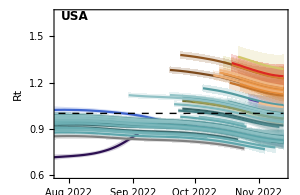
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

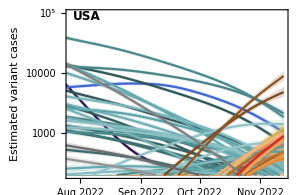
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

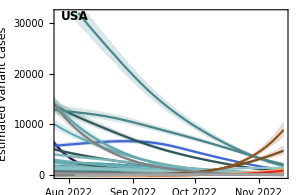
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,0.5}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

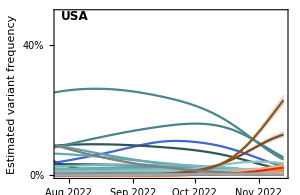
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{0.7,1.55},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

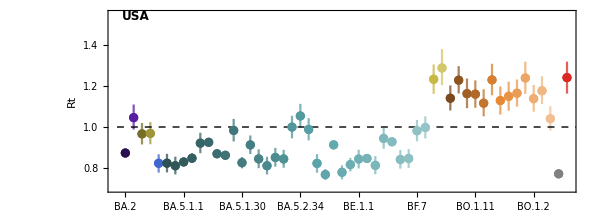

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-8]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,0.26},{0.7,1.55}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.05}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

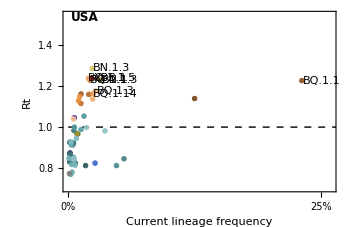
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
BN.1.3 | 1.29 | 1.2 - 1.38
XBB.1 | 1.24 | 1.16 - 1.32
BQ.1.1.5 | 1.24 | 1.16 - 1.32
BN.1 | 1.23 | 1.16 - 1.3
BQ.1.1.3 | 1.23 | 1.15 - 1.31
BQ.1.1 | 1.23 | 1.16 - 1.3
BQ.1.3 | 1.18 | 1.11 - 1.25
BQ.1.14 | 1.16 | 1.1 - 1.23

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png